## Tutorial: Haldane model

This is a notebook for the first steps for the use of the HyperBloch package for efficient modeling of tight-binding models on hyperbolic lattices.

## Preliminaries:

### Remark:

Before using the getting started with the HyperBloch notebook:

Make sure that the HyperBloch package is installed, if this is not the case please follow the instruction on the website (link to website ???).

Make sure that the required files .hcc,  .hcm and .hcs files are in the current directory. This entails files:

(2,4,6)_T2.2_3.hcc

{6,4}-tess-NNN_T2.2_3.hcm

{6,4}-tess-NNN_T2.2_3_sc-T5.4.hcs

{6,4}-tess-NNN_T2.2_3_sc-T9.3.hcs

In case no such files exists, please follow the instructions in the the prerequisites section on the website (link to website ???) or download it there.

### Load the HyperBloch package:

```mathematica
<<PatrickMLenggenhager`HyperBloch`
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

Open the documentation:

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/tutorial/BasicUsage"];
```

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/guide/HyperBlochPackage"];
```

### Needed functions:

```mathematica
ComputeEigenvalues[cfH_,Npts_,Nruns_,genus_]:=
Flatten@ParallelTable[
Flatten@Table[
Eigenvalues[cfH@@RandomReal[{-Pi,Pi},2genus]],{i,1,Round[Npts/Nruns]}],
{j,1,Nruns},Method->"FinestGrained"]
```

### Import cells

We first import the cell, model, and supercell model graphs as produced by the HyperCells package:

We consider the following sequence of supercells, defined in terms of quotients given in https://www.math.auckland.ac.nz/~conder/TriangleGroupQuotients101.txt by M. Conder, (the cell “T2.6” is the primitive cell):

```mathematica
cells={"T2.2","T5.4","T9.3"};
```

Cell graph:

```mathematica
pcell=ImportCellGraphString[Import["(2,4,6)_T2.2_3.hcc"]];
```

Primitive cell:

```mathematica
pcmodel=ImportModelGraphString[Import["{6,4}-tess-NNN_T2.2_3.hcm"]];
```

Supercells:

```mathematica
scmodels=Association[#->
ImportSupercellModelGraphString[ 
Import[ToString@StringForm["{6,4}-tess-NNN_T2.2_3_sc-``.hcs",#]]]
&/@cells[[2;;]]];
```

Extract genus:

```mathematica
genusLst={pcmodel["Genus"],(scmodels["T5.4"])["Genus"],(scmodels["T9.3"])["Genus"]};
```

### Visualize primitive cell:

Let us visualize the NN and NNN-terms of the graph representation for the next-nearest-neighbor tight-binding model on the primitive cell. They are stored as directed edges, which can be extracted from the model graph as follows:

```mathematica
EdgeList@pcmodel["Graph"]
```

{{2,1}{2,2}{1,{1,1,7}},{2,3}{2,1}{1,{2,6,12}},{2,1}{2,3}{1,{3,13,23}},{2,2}{2,4}{1,{4,2,8}},{2,4}{2,2}{1,{5,15,19}},{2,2}{2,1}{1,{6,14,24}},{2,5}{2,3}{1,{7,5,11}},{2,3}{2,5}{1,{8,18,22}},{2,4}{2,6}{1,{9,3,9}},{2,6}{2,4}{1,{10,16,20}},{2,6}{2,5}{1,{11,4,10}},{2,5}{2,6}{1,{12,17,21}},{2,1}{2,4}{2,{1,1,4}},{2,2}{2,6}{2,{1,4,9}},{2,4}{2,5}{2,{1,9,11}},{2,6}{2,3}{2,{1,11,7}},{2,5}{2,1}{2,{1,7,2}},{2,3}{2,2}{2,{1,2,1}},{2,2}{2,3}{2,{2,1,3}},{2,1}{2,5}{2,{2,3,7}},{2,3}{2,6}{2,{2,7,12}},{2,5}{2,4}{2,{2,12,9}},{2,6}{2,2}{2,{2,9,5}},{2,4}{2,1}{2,{2,5,1}},{2,4}{2,1}{2,{3,4,6}},{2,2}{2,3}{2,{3,6,2}},{2,1}{2,5}{2,{3,2,8}},{2,3}{2,6}{2,{3,8,11}},{2,5}{2,4}{2,{3,11,10}},{2,6}{2,2}{2,{3,10,4}},{2,2}{2,6}{2,{4,5,10}},{2,4}{2,5}{2,{4,10,12}},{2,6}{2,3}{2,{4,12,8}},{2,5}{2,1}{2,{4,8,3}},{2,3}{2,2}{2,{4,3,6}},{2,1}{2,4}{2,{4,6,5}}}

The first entry in the nested list above the arrow of any directed edge indicate the if the edge connects NN-vertices or NNN-vertices, indicated with integers 1 and 2, respectively.   We can visualize the corresponding edges by using the optional argument EdgeFilter of the function ShowCellGraphFlattenedpaclet:PatrickMLenggenhager/HyperBloch/ref/ShowCellGraphFlattenedPatrickMLenggenhager Package Symbol :

```mathematica
Row[
Table[
Module[{filterFunction},
filterFunction[edge_,j_]:=If[j<3,edge[[3,1]]==j,edge[[3,1]]<j];
VisualizeModelGraph[pcmodel,
Elements-><|
	ShowCellGraphFlattened->{EdgeFilter->(filterFunction[#,j]&)},
	ShowCellBoundary->{ShowEdgeIdentification->True}
|>,
CellGraph->pcell,NumberOfGenerations->3,ImageSize->300]],
{j,3}]]
```

-Graphics--Graphics--Graphics-

## {6,4} NNN tight-binding model:

### Constructing Hamiltonians:

In order to construct the Abelian Bloch Hamiltonian, we need to identify the NN and NNN-terms. Once again let us look at the list of edges in the model graph:

```mathematica
EdgeList@pcmodel["Graph"]
```

{{2,1}{2,2}{1,{1,1,7}},{2,3}{2,1}{1,{2,6,12}},{2,1}{2,3}{1,{3,13,23}},{2,2}{2,4}{1,{4,2,8}},{2,4}{2,2}{1,{5,15,19}},{2,2}{2,1}{1,{6,14,24}},{2,5}{2,3}{1,{7,5,11}},{2,3}{2,5}{1,{8,18,22}},{2,4}{2,6}{1,{9,3,9}},{2,6}{2,4}{1,{10,16,20}},{2,6}{2,5}{1,{11,4,10}},{2,5}{2,6}{1,{12,17,21}},{2,1}{2,4}{2,{1,1,4}},{2,2}{2,6}{2,{1,4,9}},{2,4}{2,5}{2,{1,9,11}},{2,6}{2,3}{2,{1,11,7}},{2,5}{2,1}{2,{1,7,2}},{2,3}{2,2}{2,{1,2,1}},{2,2}{2,3}{2,{2,1,3}},{2,1}{2,5}{2,{2,3,7}},{2,3}{2,6}{2,{2,7,12}},{2,5}{2,4}{2,{2,12,9}},{2,6}{2,2}{2,{2,9,5}},{2,4}{2,1}{2,{2,5,1}},{2,4}{2,1}{2,{3,4,6}},{2,2}{2,3}{2,{3,6,2}},{2,1}{2,5}{2,{3,2,8}},{2,3}{2,6}{2,{3,8,11}},{2,5}{2,4}{2,{3,11,10}},{2,6}{2,2}{2,{3,10,4}},{2,2}{2,6}{2,{4,5,10}},{2,4}{2,5}{2,{4,10,12}},{2,6}{2,3}{2,{4,12,8}},{2,5}{2,1}{2,{4,8,3}},{2,3}{2,2}{2,{4,3,6}},{2,1}{2,4}{2,{4,6,5}}}

#### Hopping amplitudes:

NN-terms:

```mathematica
nnVec=ConstantArray[h1,12];
```

NNN-terms:

```mathematica
nnnVec=ConstantArray[h2 ,24];
```

Construct association:

```mathematica
hoppingVec=Join[nnVec,nnnVec];
hoppingsPC=AssociationThread[EdgeList@pcmodel["Graph"]->hoppingVec];
```

#### Hamiltonians:

Primitive cell:

The Hamiltonian for the nearest-neighbor tight-binding model on the primitive cell T2.2 is:

```mathematica
Hpc=AbelianBlochHamiltonian[pcmodel,1,0&,hoppingsPC,CompileFunction->True];
```

Supercells:

The Hamiltonians for the nearest - neighbor tight - binding model on the sequence of supercells are, (this might take a minute):

```mathematica
Hclst=
Join[Association["T2.2"->Hpc],
Association[#->
AbelianBlochHamiltonian[scmodels[#],1,0&,hoppingsPC,PCModel->pcmodel,CompileFunction->True]
&/@cells[[2;;]]]];
```

### Density of states:

Let us compute the density of states by exact diagonalization.

Compute the Eigenvalues via 10^4 momentum random samples, (this might take a minute):

```mathematica
evals=Association[cells[[#]]->ComputeEigenvalues[Hclst[cells[[#]]]/.{h1->1,h2->0.05},  10^4,32,genusLst[[#]]]&/@Range[3]];
```

Visualize density of states via a kernel density estimation, (this might take a minute):

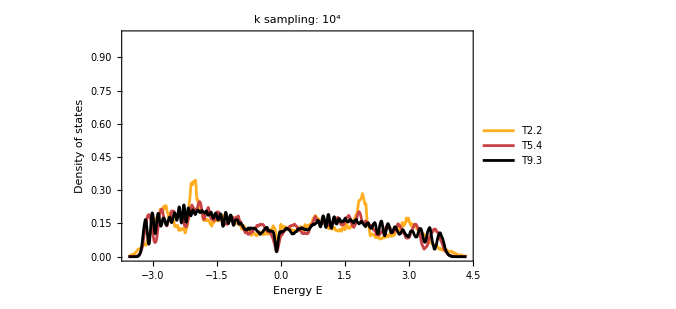

```mathematica
SmoothHistogram[evals,0.01,"PDF",Frame->True,FrameStyle->Black,FrameLabel->{"Energy E","Density of states"},PlotRange->{0,1}, LabelStyle->20,PlotLabel->"k sampling: 10^4",PlotStyle->(ColorData["SunsetColors","ColorFunction"]/@(1-Range[1,3]/3.)),ImageSize->500,ImagePadding->{{Automatic, 10}, {Automatic, 10}},Background->None]
```

## {6,4} Haldane model:

### Constructing Hamiltonians:

#### Hopping amplitudes:

#### Mass term, resp. staggered potential:

```mathematica
mVec =M0{1,-1,1,-1,1,-1};
onsitePC=AssociationThread[VertexList@pcmodel["Graph"]->mVec];
```

#### NN- and NNN-hopping terms:

```mathematica
fm=Exp[-ⅈ ϕ];fp= Exp[ⅈ ϕ] ;
```

```mathematica
nnVec=ConstantArray[h1,12];
nnnVec=ConstantArray[h2 fp,24];
hoppingVec=Join[nnVec,nnnVec];
```

```mathematica
hoppingsPC=AssociationThread[EdgeList@pcmodel["Graph"]->hoppingVec];
```

#### Hamiltonians:

Primitive cell:

The Hamiltonian for the nearest-neighbor tight-binding model on the primitive cell T2.2 is:

```mathematica
Hpc=AbelianBlochHamiltonian[pcmodel,1,onsitePC,hoppingsPC,CompileFunction->True];
```

Supercells:

The Hamiltonians for the nearest - neighbor tight - binding model on the sequence of supercells are, (this might take a minute):

```mathematica
Hclst=
Join[Association["T2.2"->Hpc],
Association[#->
AbelianBlochHamiltonian[scmodels[#],1,onsitePC,hoppingsPC,PCModel->pcmodel,CompileFunction->True]
&/@cells[[2;;]]]];
```

### Density of states:

Let us compute the density of states by exact diagonalization.

Compute the Eigenvalues via 10^4 momentum random samples, (this might take a minute):

```mathematica
evals=Association[cells[[#]]->ComputeEigenvalues[Hclst[cells[[#]]]/.{h1->1,h2->0.5, M0->0,ϕ->π/2},10^4,32,genusLst[[#]]]&/@Range[3]];
```

Visualize density of states via a kernel density estimation, (this might take a minute):

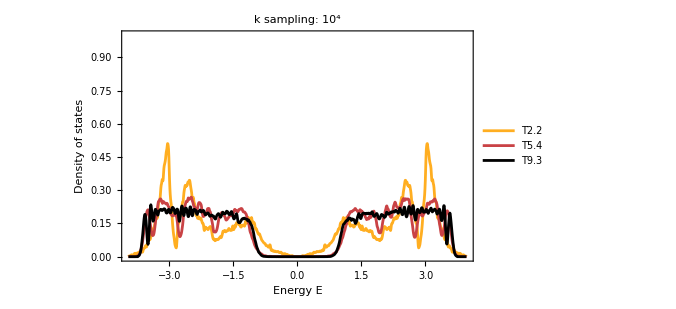

```mathematica
SmoothHistogram[evals,0.01,"PDF",Frame->True,FrameStyle->Black,FrameLabel->{"Energy E","Density of states"},PlotRange->{0,1}, LabelStyle->20,PlotLabel->"k sampling: 10^4",PlotStyle->(ColorData["SunsetColors","ColorFunction"]/@(1-Range[1,3]/3.)),ImageSize->500,ImagePadding->{{Automatic, 10}, {Automatic, 10}},Background->None]
```

```mathematica
NotebookSave[]
```